# Rosseler

Just a reminder about the Rosseler System
 https://en.wikipedia.org/wiki/R%C3%B6ssler_attractor

## Equilibria Computation and Illustration October 7th

The system has two equilbria.  One of them is easy to locate.  The other is difficult to locate  
1) The easy to see equilibrium is located in the middle of the flat portion of the attractor. It has one negative real eigenvalue a complex conjugate pair of eigenvalues with a small positive real part. The eigenvector associated with the negative real eigenvalue is almost vertical. The two dimensional invariant space associated with the complex conjugate pair of eigenvalues is almost horizontal. The negative eigenvalue compress solutions rapidly onto slow outward spirals in the almost horizontal invariant space.
2) The hard to see equilibria is well above the attractor and has a real positive eigenvalue and a complex conjugate pair of eigenvalues with a small negative real part.  The eigenvector associated with the positive real eigenvalue points down from the equilibrium down towards the attractor. The the two dimensional eigenspace for the complex conjugate pair of eigen values is roughly perpendicular to the real eigenvector. The positive real eigenvalue stretches out spirals that compress down onto the eigenvector.    
3) Solutions starting below the upper equilibria seem to get pushed down onto the attractor with the embedded lower equilibrium. Solutions  starting above the upper equilibria can get very large.

```mathematica
f[{a_,b_,c_}][{x_,y_,z_}]:= {-y-z, x + a y, b +z (x-c)}
df[{a_,b_,c_}][{x_,y_,z_}]:= {{0,-1,-1},{1,a,0},{z,0,-c+x}}
TMax=64; y0={1,2,3};
p={a,b,c}={0.2,0.2,5.7};
{eq1,eq2}=NSolveValues[f[{a,b,c}][{x,y,z}]=={0,0,0},{x,y,z}];
ySol=NDSolveValue[{
y'[t]==f[p][y[t]],
y[0]==y0
},y,{t, 0, TMax}];
ySol2=NDSolveValue[{
y'[t]==f[p][y[t]],
y[0]=={5.6929737951659,-28.464868975829496,28.4}
},y,{t, 0, TMax}];
ySol3=NDSolveValue[{
y'[t]==f[p][y[t]],
y[0]=={5.2,-28.,28.2}
},y,{t, 0, TMax}];
ySol4=NDSolveValue[{
y'[t]==f[p][y[t]],
y[0]=={5.2,-30.,31}
},y,{t, 0, TMax}];
ySol5=NDSolveValue[{
y'[t]==f[p][y[t]],
y[0]=={0.0070262048341001295,-0.035131024170500645,0.2}
},y,{t, 0, TMax}];
Show[
ParametricPlot3D[{ySol[t],ySol2[t],ySol3[t],ySol4[t],ySol5[t]},{t,0, TMax},
PlotRange->All],
Graphics3D[{PointSize[0.02],
{Red, Point[eq1],Arrow[{ eq1,eq1+5Re[v1s⟦3⟧]}],Arrow[{ eq1, eq1-5Re[v1s⟦3⟧]}]},
{Blue, Point[eq2],
Arrow[{ eq2+5Re[v2s⟦1⟧],eq2}],Arrow[{ eq2-5Re[v2s⟦1⟧],eq2}]}}],
PlotRange->30{{-1,1},{-1,1},{0,1}}
]
{λ1s,v1s}=Eigensystem[df[p][eq1]];
{λ2s,v2s}=Eigensystem[df[p][eq2]];
```

-Graphics3D-

{{0.000242166+0.187205 ⅈ,0.0344403-0.00131362 ⅈ,0.981716+0. ⅈ},{0.000242166-0.187205 ⅈ,0.0344403+0.00131362 ⅈ,0.981716+0. ⅈ},{0.00496508+0. ⅈ,-0.707577+0. ⅈ,0.706619+0. ⅈ}}

```mathematica
TMax=100;
p={a,b,c}={0.2,0.05,5.7};
{eq1,eq2}=NSolveValues[f[{a,b,c}][{x,y,z}]=={0,0,0},{x,y,z}];
{λ1s,v1s}=Eigensystem[df[p][eq1]];
{λ2s,v2s}=Eigensystem[df[p][eq2]];
ySol=NDSolveValue[{
y'[t]==f[p][y[t]],
y[0]==y0
},y,{t, 0, TMax}];
ySol2=NDSolveValue[{
y'[t]==f[p][y[t]],
y[0]=={5.6929737951659,-28.464868975829496,28.4}
},y,{t, 0, TMax}];
ySol3=NDSolveValue[{
y'[t]==f[p][y[t]],
y[0]=={5.2,-28.,28.2}
},y,{t, 0, TMax}];
ySol4=NDSolveValue[{
y'[t]==f[p][y[t]],
y[0]=={5.2,-30.,31}
},y,{t, 0, TMax}];
ySol5=NDSolveValue[{
y'[t]==f[p][y[t]],
y[0]=={0.0070262048341001295,-0.035131024170500645,0.2}
},y,{t, 0, TMax}];
Show[
ParametricPlot3D[{ySol[t],ySol2[t],ySol3[t],ySol4[t],ySol5[t]},{t,0, TMax},
PlotRange->All],
Graphics3D[{PointSize[0.02],
{Red, Point[eq1],Arrow[{ eq1,eq1+5Re[v1s⟦3⟧]}],Arrow[{ eq1, eq1-5Re[v1s⟦3⟧]}]},
{Blue, Point[eq2],
Arrow[{ eq2+5Re[v2s⟦1⟧],eq2}],Arrow[{ eq2-5Re[v2s⟦1⟧],eq2}]}}],
PlotRange->30{{-1,1},{-1,1},{0,1}}
]
```

-Graphics3D-

InterpolatingFunction[{{0., 1000.}}, <>]

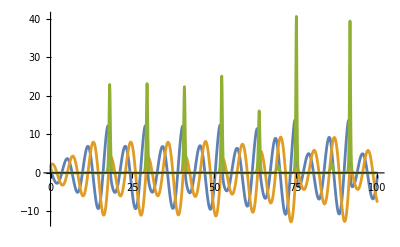

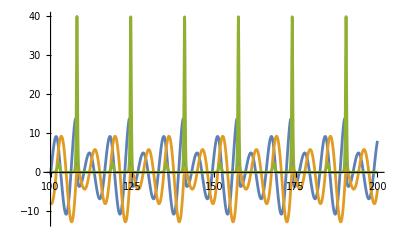

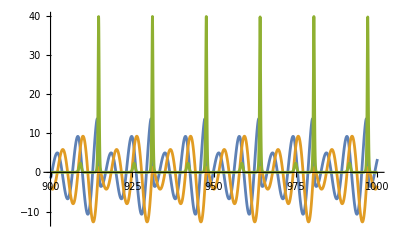

```mathematica
f[{a_,b_,c_}][{x_,y_,z_}]:= {-y-z, x + a y, b +z (x-c)}
df[{a_,b_,c_}][{x_,y_,z_}]:= {{0,-1,-1},{1,a,0},{z,0,-c+x}}
TMax=1000; y0={1,2,2};
p={a,b,c}={0.2,0.05,5.7};
{eq1,eq2}=NSolveValues[f[{a,b,c}][{x,y,z}]=={0,0,0},{x,y,z}];
{λ1s,v1s}=Eigensystem[df[p][eq1]];
{λ2s,v2s}=Eigensystem[df[p][eq2]];
ySol=NDSolveValue[{
y'[t]==f[p][y[t]],
y[0]==y0
},y,{t, 0, TMax}]
Plot[{ySol[t][[1]],ySol[t][[2]],ySol[t][[3]]},{t, 0.0 TMax,0.1 TMax},
PlotRange->All]
Plot[{ySol[t][[1]],ySol[t][[2]],ySol[t][[3]]},{t, 0.1 TMax,0.2 TMax},
PlotRange->All]
Plot[{ySol[t][[1]],ySol[t][[2]],ySol[t][[3]]},{t, 0.9 TMax, TMax},
PlotRange->All]
```

```mathematica
ParametricPlot3D[ ySol[t],{t, 100,116.4},
PlotRange->All]
```

-Graphics3D-

## Summary from Oct 7th

Generically two equilibria with d=√(-4 a b+c^2) they are 
	{1/2 (c∓d),1/2 (-c/a±d/a),(c∓d)/(2 a)}
They are real if c^2-4 a b≥0.  The Jacobian at the equilibria is
	(0 | -1 | -1
1 | a | 0
(c∓d)/(2 a) | 0 | -c+1/2 (c∓d))
The characteristic equation is 
	-λ^3+λ^2 (a-c/2∓d/2)+λ ((a c)/2-c/(2 a)+(a d)/2±d/(2 a)-1)-d=0
We can understand the eigenvalues (real, complex-conjugate pair etc.) by looking at this equation.

For the parameters we had looked at there was: 
A) An upper equilibrium with a positive real eigenvalue and a cc pair with a small negative real part. The real eigenvector associated with the positive real eigenvalue was almost vertical.
B) A lower equilibrium (in the middle of the flat bit of the attractor) with a negative real eigenvalue and a cc pair with a small positive real part. The real eigenvector associated with the negative real eigenvalue was almost vertical.

We turned down some of the parameters (following the guidance of https://en.wikipedia.org/wiki/R%C3%B6ssler_attractor) and found an attractive periodic solution that wraps around the attractor three times.

```mathematica
Clear[f,a,b,c,x,y,z,df]
f[{a_,b_,c_}][{x_,y_,z_}]:= {-y-z, x + a y, b +z (x-c)}
df[{a_,b_,c_}][{x_,y_,z_}]:= {{0,-1,-1},{1,a,0},{z,0,-c+x}}
p={a,b,c}={0.2,0.05,5.7};
TMax=1000; y0={4,5,6};
ySol=NDSolveValue[{y'[t]==f[p][y[t]],y[0]==y0},y,{t, 0, TMax}];
TabView[{
"start"->Plot[{ySol[t][[1]],ySol[t][[2]],ySol[t][[3]]},{t, 0.0 TMax,0.1 TMax},
PlotRange->All],
"end"->Plot[{ySol[t][[1]],ySol[t][[2]],ySol[t][[3]]},{t, 0.9 TMax, TMax},
PlotRange->All],
"start 3D"->ParametricPlot3D[{ySol[t][[1]],ySol[t][[2]],ySol[t][[3]]},{t, 0.0 TMax,0.1 TMax},
PlotRange->All,PlotPoints->500],
"end 3D"->ParametricPlot3D[{ySol[t][[1]],ySol[t][[2]],ySol[t][[3]]},{t, 0.9 TMax, TMax},
PlotRange->All,PlotPoints->500]}]
```

1234

We can estimate the period numerically!

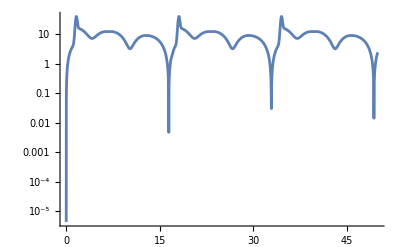

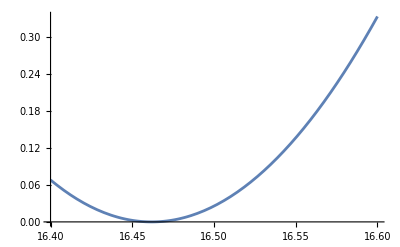

```mathematica
LogPlot[Norm[ySol[TMax]-ySol[TMax-T]],{T, 0, 50},PlotRange->All]
Plot[Norm[ySol[TMax]-ySol[TMax-T]]^2,{T,16.4,16.6}]
```

You should note that:
A) We are not worrying about how the ODE solver is doing its magic!  We are going to do some numerics in the second half of Thursdays class.
B) At this point we think we have found a periodic solution. We would like to know that with more certainty.  We are going to define “Poincare Sections” to tighten up our ability to compute periodic solutions.  https://en.wikipedia.org/wiki/Poincar%C3%A9_map
C) Just as a reminder we know how to compute the sensitivity of the  solution of an ODE with respect to the initial condition.  If f is smooth with 
	y'=f(y(t)) and y(0)=z  
along with  
	J(t)=df(y(t)).J(t) and J(0)=Id 
then J(t)=∂_z y(t).